## Equilibrium and stability analysis for nonlinear autonomous systems

Katharine Long, TTU

### Define the RHS of a system of ODEs

```mathematica
F[x_,y_]={x - y x^2, x y -y}
```

{x-x^2 y,x y-y}

#### Find equilibrium points

```mathematica
Solve[F[x,y]=={0,0},{x,y}]
```

{{x→1,y→1},{x→0,y→0}}

#### Compute the Jacobian

```mathematica
J[x_,y_]=Table[D[F[x,y][[i]],ξ],{i,1,2},{ξ,{x,y}}]
```

(1-2 x y | -x^2
y | x-1)

```mathematica
J1 = J[0,0]
```

(1 | 0
0 | -1)

```mathematica
J2=J[1,1]
```

(-1 | -1
1 | 0)

```mathematica
Eigenvalues[J2]
```

{--1^(1/3),(-1)^(2/3)}

```mathematica
N[Eigenvalues[J2]]
```

{-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ}

#### View solutions

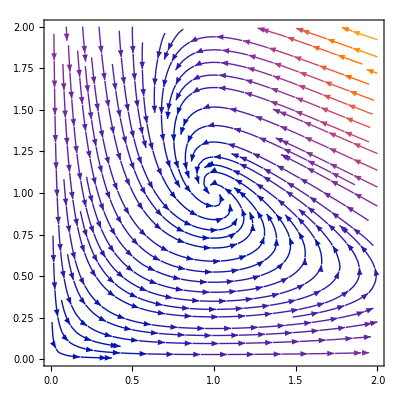

```mathematica
StreamPlot[F[x,y],{x,0,2},{y,0,2}]
```

## A coexisting competing species model

From Boyce & DiPrima, Example 1 in 9.4.

```mathematica
G[x_,y_]={x(1-x-y),y(3/4-y-1/2 x)}
```

{x (-x-y+1),y (-x/2-y+3/4)}

```mathematica
Solve[G[x,y]=={0,0},{x,y}]
```

{{x→0,y→3/4},{x→1/2,y→1/2},{x→1,y→0},{x→0,y→0}}

```mathematica
J[x_,y_]=Table[D[G[x,y][[i]],ξ],{i,1,2},{ξ,{x,y}}]
```

(-2 x-y+1 | -x
-y/2 | -x/2-2 y+3/4)

```mathematica
J1=J[0,3/4]
```

(1/4 | 0
-3/8 | -3/4)

```mathematica
J2=J[1/2,1/2]
```

(-1/2 | -1/2
-1/4 | -1/2)

```mathematica
Eigenvalues[J2]
```

{1/4 (-2-√2),1/4 (√2-2)}

```mathematica
J3 = J[1,0]
```

(-1 | -1
0 | 1/4)

```mathematica
J4=J[0,0]
```

(1 | 0
0 | 3/4)

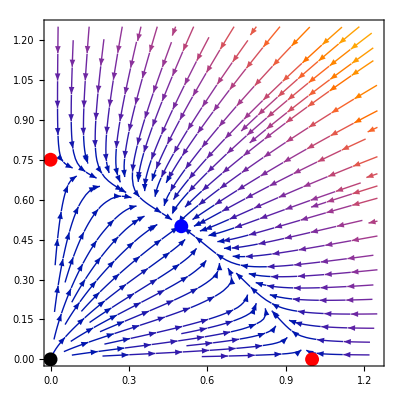

```mathematica
StreamPlot[G[x,y],{x,0,5/4},{y,0,5/4},
Epilog->{PointSize[0.025],
{Red,Point[{0,3/4}], Point[{1,0}]},(* saddles *)
{Blue, Point[{1/2,1/2}]},(* attractor *){Black,Point[{0,0}] } (* repellor *)}
]
```

## A damped pendulum

```mathematica
PEND[γ_,x_,v_]={v,-Sin[x]-γ v}
```

{v,γ (-v)-sin(x)}

```mathematica
showPend[γ_]:=StreamPlot[PEND[γ,x,v],{x,-3Pi, 3Pi},{v,-4,4},
StreamPoints->Fine,
Epilog->{PointSize[0.025],
{Red,Point[{-Pi,0}], Point[{Pi,0}]},(* saddles *)
{Blue, Point[{-2Pi,0}],Point[{0,0}],Point[{2Pi,0}]}(* attractors *)}
]
```

```mathematica
Manipulate[showPend[γ],{γ,0,1}]
```

## Van der Pol equation

Solution goes to a limit cycle

```mathematica
VDP[γ_,x_,v_]={v,-x + γ (1-x^2)v}
```

{v,γ v (1-x^2)-x}

```mathematica
showVDP[γ_]:=StreamPlot[VDP[γ,x,v],{x,-6,6},{v,-6,6},
StreamPoints->Fine,
Epilog->{PointSize[0.025],
{Black, Point[{0,0}]}(* repellors *)}
]
```

```mathematica
Manipulate[showVDP[γ],{γ,0,1,1/16}]
```

```mathematica
vdpSoln[γ_,t_]:=y[t]/. NDSolve[{y''[t]-γ y'[t](1-y[t]^2)+y[t]==0, y[0]==5, y'[0]==0},y[t], {t, 0, 60Pi}][[1]]
```

```mathematica
ySoln1[t_]=vdpSoln[1,t]
```

InterpolatingFunction[…](t)

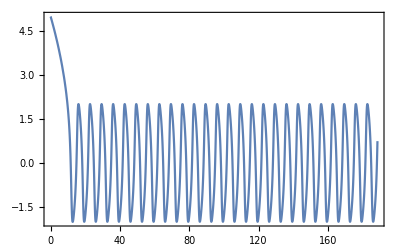

```mathematica
Plot[ySoln1[t],{t,0,60Pi},PlotRange->All]
```

```mathematica
Evaluate[{ySoln1[1],ySoln1'[1]}]
```

(0.00524858
-0.00885008)

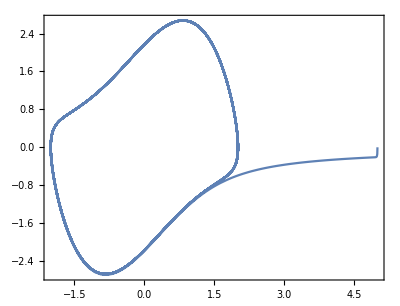

```mathematica
ParametricPlot[Evaluate[{ySoln1[t],ySoln1'[t]}],{t,0,50Pi}]
```